# UniDyn--Demo-08.nb

John A. Marohn
jam99@cornell.edu
Cornell University

Abstract:  This demonstration notebook performs a quantum optics calculation.

## Set the path to the package

Check the Mathematica version number .

```mathematica
$VersionNumber
```

12.3

Tell Mathematica the path to the directory containing the packages and the /studies directory. 

EDIT THE FOLLOWING PATH STRINGS:

```mathematica
$UniDynPath ="/Users/jam99/Dropbox/MarohnGroup__Software_Library/UniDyn/unidyn";
```

YOU SHOULD NOT NEED TO EDIT ANYTHING FROM HERE ONWARDS.

## Load and test the packages

### Load Unidyn

Append the package path to the system path.  Before trying to load the package, ask Mathematica to find it.  This is a test that we directed Mathematica to the correct directory.  The output of this command should be the full system path to the UniDyn.m file.

```mathematica
$Path = AppendTo[$Path,$UniDynPath];
FindFile["UniDyn`"]
```

/Users/jam99/Dropbox/MarohnGroup__Software_Library/UniDyn/unidyn/UniDyn.m

Now that we are confident that the path is set correctly, load the Unidyn package.  
Setting the global $VerboseLoad variable to True will print out the help strings for key commands in the package.

```mathematica
$VerboseLoad =True;
Needs["UniDyn`"]
```

### Run the Unidyn unit tests

Carry out the unit tests for the Unidyn functions.

```mathematica
SetDirectory[$UniDynPath];
```

```mathematica
fn = FileNames["*-tests.m"];
test$report =TestReport /@ fn;
TableForm[Table[test$report [[k]],{k,1,Length[test$report]}]]
```

TestReportObject[…]
TestReportObject[…]
TestReportObject[…]
TestReportObject[…]
TestReportObject[…]
TestReportObject[…]
TestReportObject[…]
TestReportObject[…]
TestReportObject[…]
TestReportObject[…]

## Evolver settings

Choose which Evolver to use.

```mathematica
Evolver=Evolver2;
```

## Two two-level systems coupled to a common cavity

Clear all the symbols; start afresh.

```mathematica
Clear[Ix, Iy, Iz, Ip, Im,Sx, Sy, Sz, Sp, Sm, aR, aL];
Clear[ω,ω$I, ω$S, g$I, g$S, Δ, n];
Clear[H$0 ,H$1];
```

Clear::wrsym: Symbol Im is Protected.

Create pseudo-spin operators for an I atom and an S atom.
Create raising and lowering operators for the single-mode cavity.

```mathematica
TwoSpinBoson$CreateOperators[Ix, Iy, Iz, I$p, I$m,Sx, Sy, Sz, S$p, S$m,aR, aL];
```

SpinSingle$CreateOperators::nocreate: Spin operators already exist.

SpinSingle$CreateOperators::comm: Adding spin commutations relations.

SpinSingle$CreateOperators::simplify: Angular momentum L = 1/2. Adding operator simplification rules.

SpinSingle$CreateOperators::nocreate: Spin operators already exist.

SpinSingle$CreateOperators::comm: Adding spin commutations relations.

SpinSingle$CreateOperators::simplify: Angular momentum L = 1/2. Adding operator simplification rules.

OscSingle$CreateOperators::nocreate: Oscillator operators already exist.

OscSingle$CreateOperators::comm: Adding oscillator commutations relations.

TwoSpinBoson$CreateOperators::create: Creating operators.

TwoSpinBoson$CreateOperators::comm: Adding Ip, Im and Sp, Sm commutations relations.

TwoSpinBoson$CreateOperators::simp: Adding Ip, Im and Sp, Sm simplification rules.

TwoSpinBoson$CreateOperators::normord: Adding aL and aR normal ordering rule.

Scalar parameters appearing the Hamiltonians .

```mathematica
CreateScalar[
ω,     (* cavity frequency *)
ω$I, (* atom I frequency *)
ω$S, (* atom S frequency *)
g$I, (* unitless coupling constant characterizing the interaction of atom I with the cavity mode  *)
g$S, (* unitless coupling constant characterizing the interaction of atom I with the cavity mode  *)
Δ         (* resonance offset *)
]
```

Hamiltonian for the bare atoms I and S and the cavity.

```mathematica
H$0 = ω$I Iz + ω$S Sz + ω Mult[aR, aL];
```

Coupling Hamiltonian describing the exchange of photons between atom I and the cavity and atom S and the cavity.

```mathematica
H$1 = g$I ω (Mult[I$p,aL] + Mult[I$m, aR]) + g$S ω (Mult[S$p,aL] + Mult[S$m, aR]);
```

### Version 1

The cavity frequency is ω, atom I has resonance frequency ω (in tune with the cavity resonance), and atom S has resonance frequency ω - Δ (detuned from the cavity resonance by an amount Δ).  Here atoms I and S are different Species.

Take the coupling Hamiltonian into the interaction representation:

```mathematica
Clear[H$1$int];
H$1$int[t_]=(Evolve[H$0,t,H$1]  /. Evolve-> Evolver2) /. {ω$I -> ω, ω$S -> ω - Δ} // Simplify // Expand
```

g$I ω Mult[I$m,aR]+g$I ω Mult[I$p,aL]+ⅇ^(-ⅈ t Δ) g$S ω Mult[S$m,aR]+ⅇ^(ⅈ t Δ) g$S ω Mult[S$p,aL]

Using the Magnus expansion, compute a zeroth-order average Hamiltonian:

```mathematica
H$1$int$0 = 1/t$c Integrate[H$1$int[t],{t,0,t$c}] /. t$c -> (2 π)/Δ// Expand
```

g$I ω Mult[I$m,aR]+g$I ω Mult[I$p,aL]

To zeroth order, only atom I is coupled to the cavity.

Using the Magnus expansion, compute a first-order average Hamiltonian:

```mathematica
H$1$int$1 = -I/(2 t$c)Integrate[Integrate[Comm[H$1$int[t1],H$1$int[t2]],{t1, 0,t2}],{t2,0,t$c}] /. t$c-> (2 π)/Δ
```

-1/(8 π Δ)ⅈ g$S ω^2 (-4 ⅈ g$S π-8 ⅈ g$S π Sz+4 ⅈ g$I π Mult[S$m,I$p]+4 ⅈ g$I π Mult[S$p,I$m]-16 ⅈ g$S π Mult[Sz,aR,aL]+2 g$I Mult[I$m,S$p] (1-Cos[2 π √(1/Δ^2) Abs[Δ]]+(2 π (ⅈ Cos[2 π √(1/Δ^2) Abs[Δ]] Sign[Δ]-Sin[2 π √(1/Δ^2) Abs[Δ]]))/(√(1/Δ^2) Abs[Δ])-ⅈ Sign[Δ] Sin[2 π √(1/Δ^2) Abs[Δ]])+(2 g$I Mult[I$p,S$m] ((2 π (ⅈ Cos[2 π √(1/Δ^2) Abs[Δ]] Sign[Δ]+Sin[2 π √(1/Δ^2) Abs[Δ]]))/(√(1/Δ^2))+Abs[Δ] (-1+Cos[2 π √(1/Δ^2) Abs[Δ]]-ⅈ Sign[Δ] Sin[2 π √(1/Δ^2) Abs[Δ]])))/Abs[Δ])

Simplify the first-order average Hamiltonian by assuming that the resonance offset is positive.  
Use sorted multI$plication to put the I and S angular momentum operators in canonical order, with the I-atom operators first and the S-atom operators second.

```mathematica
ans1 = Expand[Simplify[H$1$int$1,Assumptions-> {Element[Δ,Reals], Δ > 0}]] /. {Mult -> SortedMult}
```

-(g$S^2 ω^2)/(2 Δ)-(g$S^2 Sz ω^2)/Δ+(g$I g$S ω^2 Mult[I$m,S$p])/Δ+(g$I g$S ω^2 Mult[I$p,S$m])/Δ-(2 g$S^2 ω^2 Mult[Sz,aR,aL])/Δ

```mathematica
Collect[ans1 ,ω^2/Δ]
```

(ω^2 (-g$S^2/2-g$S^2 Sz+g$I g$S Mult[I$m,S$p]+g$I g$S Mult[I$p,S$m]-2 g$S^2 Mult[Sz,aR,aL]))/Δ

There are two physical effects contributed by the first-order terms.

	1) A shift in the atom S energy levels, proportional to (n + 1/2), with n the number of photons in the cavity.
	2) A coupling between atoms I and S of the form I_- S_++I_+S_-.

The coherence I_+ will evolve under this Hamiltonian into I_+Cos[Ω t] + 2 i I_z S_+ Sin[Ω t], entangling the electronic states of atoms I and S.

```mathematica
Evolve[Ω (Mult[I$m,S$p] + Mult[I$p,S$m]), t, I$p]  /. Evolve -> Evolver2
```

I$p Cos[t Ω]+2 ⅈ Mult[Iz,S$p] Sin[t Ω]

### Version 2

The cavity frequency is ω and atom I and S each has a resonance frequency ω - Δ (detuned from the cavity resonance by an amount Δ).  
Here atoms I and S are the same species.

Take the coupling Hamiltonian into the interaction representation:

```mathematica
Clear[H$1$int];
H$1$int[t_]=(Evolve[H$0,t,H$1]  /. Evolve-> Evolver2) /. {ω$I -> ω - Δ, ω$S -> ω - Δ} // Simplify // Expand
```

ⅇ^(-ⅈ t Δ) g$I ω Mult[I$m,aR]+ⅇ^(ⅈ t Δ) g$I ω Mult[I$p,aL]+ⅇ^(-ⅈ t Δ) g$S ω Mult[S$m,aR]+ⅇ^(ⅈ t Δ) g$S ω Mult[S$p,aL]

Using the Magnus expansion, compute a zeroth-order average Hamiltonian:

```mathematica
H$1$int$0 =Expand[ 1/t$c Integrate[H$1$int[t],{t,0,t$c}] /. t$c -> (2 π)/Δ]
```

0

To zeroth order, the irradiation now has no effect.
The Hamiltonian does not commute with itself at different times.

```mathematica
Comm[H$1$int[t1],H$1$int[t2]]
```

-ⅇ^(-ⅈ t1 Δ+ⅈ t2 Δ) g$I g$S ω^2 Mult[I$m,S$p]+ⅇ^(ⅈ t1 Δ-ⅈ t2 Δ) g$I g$S ω^2 Mult[I$p,S$m]-ⅇ^(-ⅈ t1 Δ+ⅈ t2 Δ) g$I g$S ω^2 Mult[S$m,I$p]+ⅇ^(ⅈ t1 Δ-ⅈ t2 Δ) g$I g$S ω^2 Mult[S$p,I$m]+ⅇ^(ⅈ t1 Δ-ⅈ t2 Δ) g$I^2 ω^2 (1/2+Iz+2 Mult[Iz,aR,aL])+ⅇ^(-ⅈ t1 Δ+ⅈ t2 Δ) g$I^2 ω^2 (-1/2+Iz-2 (Iz+Mult[Iz,aR,aL]))+ⅇ^(ⅈ t1 Δ-ⅈ t2 Δ) g$S^2 ω^2 (1/2+Sz+2 Mult[Sz,aR,aL])+ⅇ^(-ⅈ t1 Δ+ⅈ t2 Δ) g$S^2 ω^2 (-1/2+Sz-2 (Sz+Mult[Sz,aR,aL]))

Using the Magnus expansion, compute a first-order average Hamiltonian:

```mathematica
H$1$int$1 = -I/(2 t$c)Integrate[Integrate[Comm[H$1$int[t1],H$1$int[t2]],{t1, 0,t2}],{t2,0,t$c}] /. t$c-> (2 π)/Δ
```

-1/(8 π Δ)ⅈ ω^2 (-4 ⅈ π (g$I^2 (1+2 Iz)+g$S^2 (1+2 Sz))-2 g$I (g$S (Mult[I$p,S$m]+Mult[S$p,I$m])+2 g$I Mult[Iz,aR,aL])-4 g$S^2 Mult[Sz,aR,aL]+2 (g$I (g$S (Mult[I$m,S$p]+Mult[S$m,I$p])+2 g$I Mult[Iz,aR,aL])+2 g$S^2 Mult[Sz,aR,aL])-2 ⅈ (g$I (g$S ((-ⅈ+2 π) Mult[I$m,S$p]+ⅈ (Mult[I$p,S$m]-Mult[S$m,I$p]+Mult[S$p,I$m])+2 π (Mult[I$p,S$m]+Mult[S$m,I$p]+Mult[S$p,I$m]))+8 g$I π Mult[Iz,aR,aL])+8 g$S^2 π Mult[Sz,aR,aL]))

Use sorted multI$plication to put the I and S angular momentum operators in canonical order, with the I-atom operators first and the S-atom operators second.

```mathematica
ans2 = (H$1$int$1 // Expand )/. {Mult -> SortedMult}
```

-(g$I^2 ω^2)/(2 Δ)-(g$S^2 ω^2)/(2 Δ)-(g$I^2 Iz ω^2)/Δ-(g$S^2 Sz ω^2)/Δ-(g$I g$S ω^2 Mult[I$m,S$p])/Δ-(g$I g$S ω^2 Mult[I$p,S$m])/Δ-(2 g$I^2 ω^2 Mult[Iz,aR,aL])/Δ-(2 g$S^2 ω^2 Mult[Sz,aR,aL])/Δ

```mathematica
Collect[ans2 ,-ω^2/Δ]
```

-(g$I^2 ω^2)/(2 Δ)-(g$S^2 ω^2)/(2 Δ)-(ω^2 (g$I^2 Iz+g$S^2 Sz+g$I g$S Mult[I$m,S$p]+g$I g$S Mult[I$p,S$m]))/Δ-(2 g$I^2 ω^2 Mult[Iz,aR,aL])/Δ-(2 g$S^2 ω^2 Mult[Sz,aR,aL])/Δ

There are three physical effects contributed by the first-order terms.

	1) A shift in the atom S energy levels, proportional to (n + 1/2), with n the number of photons in the cavity.
	2) A shift in the atom I energy levels, proportional to (n + 1/2), with n the number of photons in the cavity.
	3) A coupling between atoms I and S of the form I_- S_++I_+S_-.
	
Write an effective Hamiltonian assuming there are  n = 0 photons in the cavity, so that

	 I_z a^†a⟶ I_z n ⟶ 0  
	 S_z a^†a⟶ S_z n ⟶ 0  
	
Also set

	g_I⟶ g
	g_I⟶ g 

and write I_(+/-) and  S_(+/-) in terms of the associated x and y angular momentum operators.

```mathematica
H$eff = Simplify[-(ω^2 (g$I^2 Iz+g$S^2 Sz+g$I g$S Mult[I$m,S$p]+g$I g$S Mult[I$p,S$m]))/Δ /.
 { g$I -> g, g$S -> g,
I$p -> Ix + I Iy, I$m -> Ix - I Iy, 
S$p -> Sx + I Sy, S$m -> Sx - I Sy}
];
H$eff = H$eff/. (g^2 ω^2)/Δ -> Ω
```

-Ω (Iz+Sz+2 Mult[Ix,Sx]+2 Mult[Iy,Sy])

Let us calculate the evolution of the full density operator

	ρ(0^+)=(1/2+I_x)(1/2+S_x)
	
This initial density operator can be created by applying a π/2 pulse to both atoms, cooled to their ground state.

	ρ(0)=(1/2+I_z)(1/2+S_z)

```mathematica
ρ$0 = Mult[1/2+Iz,1/2+Sz];
```

```mathematica
ρ$init = Evolve[w (Sy + Iy),1/w π/2,ρ$0 ]  /. Evolve -> Evolver2
```

1/4+Ix/2+Sx/2+Mult[Ix,Sx]

Evolve this initial density operator under the effective Hamiltonian

```mathematica
ρ1 = (Evolve[H$eff ,t,ρ$init] /. Evolve -> Evolver1 )/. Mult-> SortedMult  // Simplify // Expand
```

1/4+Ix/4+Sx/4+1/4 Ix Cos[2 t Ω]+1/4 Sx Cos[2 t Ω]+Cos[t Ω]^2 Mult[Ix,Sx]+Mult[Ix,Sz] Sin[t Ω]^2+Mult[Iy,Sy] Sin[t Ω]^2+Mult[Iz,Sx] Sin[t Ω]^2-1/4 Iy Sin[2 t Ω]-1/4 Sy Sin[2 t Ω]-1/2 Mult[Ix,Sy] Sin[2 t Ω]-1/2 Mult[Iy,Sx] Sin[2 t Ω]+1/2 Mult[Iy,Sz] Sin[2 t Ω]+1/2 Mult[Iz,Sy] Sin[2 t Ω]

Check that we recover the initial density operator at time zero. 
We show below by looking at the ρ1 matrix, that the associated wavefunction is simply

	|↑↑⟩
	
which is what we expect for the system in it ground state.

```mathematica
ρ1 /. {t -> 0} // Expand
```

1/4+Ix/2+Sx/2+Mult[Ix,Sx]

Compute the post-interaction density operator at a time at which the equivalent pulse angle is π/2.  
We will show below, numerically, that this is a maximally entangled state of the two qubits.
The post-interaction density operator corresponds to a wavefunction of 

	1/2( ↑↑- ↑↓-↓↑-↓↓) 
	
which we determined with the help of Anthropic’s Claude AI.

```mathematica
ρ1$special = ρ1/. {t-> π/2 1/Ω} // Simplify
```

1/4+Mult[Ix,Sz]+Mult[Iy,Sy]+Mult[Iz,Sx]

Load the matrices for two spin 1/2 particles.

```mathematica
<<Matrices--two-spin-half.m
```

Loaded spin one-half matrices for mIx, mIy, mIz, mSx, mSy, mSz

Write the density operator in matrix form.  

This is tricky.  The “constant”, non-operator, part of the density operator should be replaced by the 4 x 4 unit matrix (i.e., IdentityMatrix[4]).  In the code below we use the function ScalarPart[] to extract the scalar, non-operator part of the density operator.  Multiply this scalar part by the symbol Id (which we will substitute with IdentityMatrix[4]) and add it back to the remainder of the density operator.  Convert the result to matrix form using a set of substitutions.

```mathematica
rules1 = {Mult->Dot};
rules2 = {Id -> IdentityMatrix[4], Ix->mIx,Iy->mIy,Iz->mIz,Sx->mSx,Sy->mSy,Sz->mSz};

ScalarPart[expr_]:=Total[Select[List@@Expand[expr],FreeQ[#,_?OperatorQ]&]]

matrixify[rho_] :=Module[{scalarpart, rho$, rho$matrix},
scalar = ScalarPart[rho];
nonscalar = rho - scalar;
 rho$ = scalar * Id + nonscalar;
rho$matrix = Simplify[(rho$ /. rules1) /. rules2];
Print["Tr[ρ] = ", Simplify[Tr[rho$matrix]]];
Print["Tr[ρ^2] = ", Simplify[Tr[rho$matrix  . rho$matrix]]];
Return[rho$matrix]
]
```

Verify by inspection that the matrixify[] function works correctly on the initial density operator.
The atomic subsystems should be in the ground-state wavefunction |↑↑⟩  and we can verify that this is so by inspection.
We can also see that the initial density operator has unit trace, and its square has unit trace.

```mathematica
ρ$0
```

1/4+Iz/2+Sz/2+Mult[Iz,Sz]

```mathematica
ρ$0$mat = matrixify[ρ$0];
ρ$0$mat// MatrixForm
```

Tr[ρ] = 1

Tr[ρ^2] = 1

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)

As expected for a density operator, the special matrix also has unit trace and its square has unit trace.

```mathematica
ρ1$special$mat = matrixify[ρ1$special];
ρ1$special$mat // MatrixForm
```

Tr[ρ] = 1

Tr[ρ^2] = 1

(1/4 | -1/4 | -1/4 | -1/4
-1/4 | 1/4 | 1/4 | 1/4
-1/4 | 1/4 | 1/4 | 1/4
-1/4 | 1/4 | 1/4 | 1/4)

A measure of the entanglement of two qubits is the value of the Wootters’ concurrence function, doi:10.1103/PhysRevLett.80.2245.
The following concurrent-computing function was developed in collaboration with Anthropic’s Claude AI.

```mathematica
Concurrence[rho_]:=Module[{sy,rhoTilde,R,eigs},
sy={{0,-I},{I,0}};
rhoTilde=KroneckerProduct[sy,sy].Conjugate[rho].KroneckerProduct[sy,sy];
R=rho.rhoTilde; 
eigs=Sqrt[Sort[Re[Chop[Eigenvalues[R]]],Greater]];
Max[0,eigs[[1]]-eigs[[2]]-eigs[[3]]-eigs[[4]]]]
```

```mathematica
rho$test={{0,0,0,0},{0,1/2,-1/2,0},{0,-1/2,1/2,0},{0,0,0,0}};
ConcurrenceSymbolic[rho$test]
```

1

The initial density operator is a pure state, with a Wootters’ concurrence of 0.

```mathematica
Concurrence[ρ$0$mat]
```

0

The density operator following the timed interaction is a maximally entangled state, with a Wootters’ concurrence of 1.

```mathematica
Concurrence[ρ1$special$mat]
```

1

Let us calculate the Wootters’ concurrence at any interaction time (i.e, pulse angle).
Rewrite the post-interaction density operator in terms of pulse angle instead of interaction time.

```mathematica
Clear[θ];
ρ1$mat = matrixify[ρ1] /. {t Ω -> θ};
ρ1$mat // MatrixForm
```

Tr[ρ] = 1

Tr[ρ^2] = 1

(1/4 | 1/4 (Cos[2 θ]-ⅈ Sin[2 θ]) | 1/4 (Cos[2 θ]-ⅈ Sin[2 θ]) | 1/4 (Cos[2 θ]-ⅈ Sin[2 θ])
1/4 (Cos[2 θ]+ⅈ Sin[2 θ]) | 1/4 | 1/4 | 1/4
1/4 (Cos[2 θ]+ⅈ Sin[2 θ]) | 1/4 | 1/4 | 1/4
1/4 (Cos[2 θ]+ⅈ Sin[2 θ]) | 1/4 | 1/4 | 1/4)

The function f computes the concurrence as function of pulse angle.

```mathematica
f[t_] := Concurrence[ρ1$mat /. {θ -> 2 π t}]
```

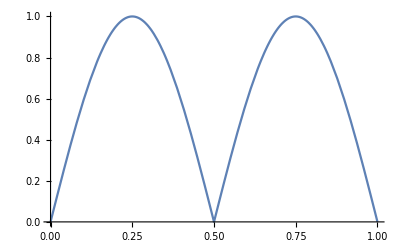

```mathematica
Plot[f[t],{t,0,1}]
```

We can see that the concurrence is 1 when t is 0.25 and 0.75, corresponding to pulse angles  of π/2 and 3π/2.

```mathematica
{Concurrence[ρ1$mat /. {θ -> π/2}],
Concurrence[ρ1$mat /. {θ -> π/2}]}
```

{1,1}

## Clean up

```mathematica
resetVariables=False; (* Set to True to reset variable and to False to NOT reset the variables *)

If[resetVariables,
Clear[Ix,Iy,Iz,I$p,I$m,Sx,Sy,Sz,S$p,S$m,aR,aL];
Clear[ω,ω$I,ω$S,g$I,g$S,Δ, n];
Clear[H$0,H$1];
]
```